```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
mub={0,300,400,500,550,575,600};
fitdata=Table[Import["./mub"<>ToString[mub[[i]]]<>".dat"],{i,1,Length[mub]}];
```

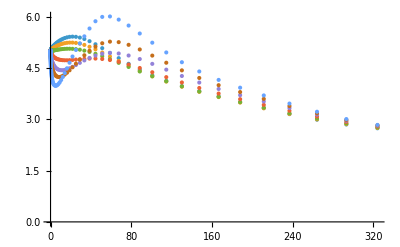

```mathematica
ListPlot[fitdata,PlotRange->All]
```

```mathematica
fitfun=Table[Interpolation[fitdata[[i]]],{i,1,Length[mub]}];
```

```mathematica
T0p01=Table[Flatten[FindRoot[Abs[(fitfun[[i]][x]-5)/5]==0.01,{x,0.01,fitdata[[1]][[1]][[1]],fitdata[[1]][[-1]][[1]]}],2][[1]][[2]],{i,1,Length[mub]}]
Export["delta0p01.dat",T0p01];
T0p02=Table[Flatten[FindRoot[Abs[(fitfun[[i]][x]-5)/5]==0.02,{x,0.01,fitdata[[1]][[1]][[1]],fitdata[[1]][[-1]][[1]]}],2][[1]][[2]],{i,1,Length[mub]}]
Export["delta0p02.dat",T0p02];
T0p03=Table[Flatten[FindRoot[Abs[(fitfun[[i]][x]-5)/5]==0.03,{x,0.01,fitdata[[1]][[1]][[1]],fitdata[[1]][[-1]][[1]]}],2][[1]][[2]],{i,1,Length[mub]}]
Export["delta0p03.dat",T0p03];
```

{0.590649,1.3446,11.414,0.25237,0.0481776,0.018054,0.00509723}

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法使优化目标函数的值减小得足够多. 您可能需要多于 MachinePrecision 位的工作精度以满足这些容差.

{1.70885,3.6798,18.0889,0.925543,0.167908,0.0620902,0.0166705}

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法使优化目标函数的值减小得足够多. 您可能需要多于 MachinePrecision 位的工作精度以满足这些容差.

{3.13011,6.73344,18.0889,2.10064,0.357484,0.130995,0.0347935}

```mathematica
Export["mub2.dat",mub]
```

mub2.dat

```mathematica
mub2={0,100,200,300,400,500,550,575,600}
```

{0,100,200,300,400,500,550,575,600}

```mathematica
f=Interpolation[Transpose[{mub,T}],InterpolationOrder->1]
```

Transpose::nmtx: {{0,300,400,500,550,575,600},T} 的前两层无法转置.

Interpolation::innd: { 中的第一个参数不包含数据和坐标列表.

Interpolation[Transpose[{{0,300,400,500,550,575,600},T}],InterpolationOrder→1]

```mathematica
ListPlot[Table[{x,f[x]},{x,0,600,50}],ScalingFunctions->{Automatic"Log"},PlotRange->All]
```

Transpose::nmtx: {{0,300.,400.,500.,550.,575.,600.},T} 的前两层无法转置.

Interpolation::innd: { 中的第一个参数不包含数据和坐标列表.

Transpose::nmtx: {{0.,300.,400.,500.,550.,575.,600.},T} 的前两层无法转置.

Interpolation::innd: { 中的第一个参数不包含数据和坐标列表.

Transpose::nmtx: {{0.,300.,400.,500.,550.,575.,600.},T} 的前两层无法转置.

General::stop: 在本次计算中，Transpose::nmtx 的进一步输出将被抑制.

Interpolation::innd: { 中的第一个参数不包含数据和坐标列表.

General::stop: 在本次计算中，Interpolation::innd 的进一步输出将被抑制.

ListPlot::sclfn: 缩放函数 {Log Automatic} 不能用来缩放坐标.

-Graphics-

```mathematica
Table[f[mub2[[i]]],{i,1,Length[mub2]}]
Export["delta0p01.dat",%];
```

{Interpolation[Transpose[{{0,300,400,500,550,575,600},T}],InterpolationOrder→1][0],Interpolation[Transpose[{{0,300,400,500,550,575,600},T}],InterpolationOrder→1][100],Interpolation[Transpose[{{0,300,400,500,550,575,600},T}],InterpolationOrder→1][200],Interpolation[Transpose[{{0,300,400,500,550,575,600},T}],InterpolationOrder→1][300],Interpolation[Transpose[{{0,300,400,500,550,575,600},T}],InterpolationOrder→1][400],Interpolation[Transpose[{{0,300,400,500,550,575,600},T}],InterpolationOrder→1][500],Interpolation[Transpose[{{0,300,400,500,550,575,600},T}],InterpolationOrder→1][550],Interpolation[Transpose[{{0,300,400,500,550,575,600},T}],InterpolationOrder→1][575],Interpolation[Transpose[{{0,300,400,500,550,575,600},T}],InterpolationOrder→1][600]}

```mathematica
ListPlot[Transpose[{mub2,f[mub2]}]]
```

Transpose::nmtx: {{0,100,200,300,400,500,550,575,600},Interpolation[{,InterpolationOrder→1][{0,100,200,300,400,500,550,575,600}]} 的前两层无法转置.

Transpose::nmtx: {{0,100.,200.,300.,400.,500.,550.,575.,600.},Interpolation[{,InterpolationOrder→1.][{0,100.,200.,300.,400.,500.,550.,575.,600.}]} 的前两层无法转置.

Transpose::nmtx: {{0.,300.,400.,500.,550.,575.,600.},T} 的前两层无法转置.

General::stop: 在本次计算中，Transpose::nmtx 的进一步输出将被抑制.

Interpolation::innd: { 中的第一个参数不包含数据和坐标列表.

ListPlot::lpn: { 不是由数字或者数对组成的列表.

ListPlot[Transpose[{{0,100,200,300,400,500,550,575,600},Interpolation[Transpose[{{0,300,400,500,550,575,600},T}],InterpolationOrder→1][{0,100,200,300,400,500,550,575,600}]}]]

```mathematica
fitdata[[1]][[-1]]
```

{324.229,2.73635}